```mathematica
path = FileNameJoin[Drop[#,Flatten@{Position[#,"Master"]+1,-1}]&@StringSplit[NotebookDirectory[],"\\"]];
```

```mathematica
ClearAll[data11, data12, data15]
data11=Table[Import[path<>"\\Data\\2017\\may\\11\\may11_"<>ToString[i]<>".dat"],{i,6,9}];
data12=Table[Import[path<>"\\Data\\2017\\may\\12\\may12_"<>ToString[i]<>".dat"],{i,2,4}];
data15=Table[Import[path<>"\\Data\\2017\\may\\15\\may15_"<>ToString[i]<>".dat"],{i,3,6}];
```

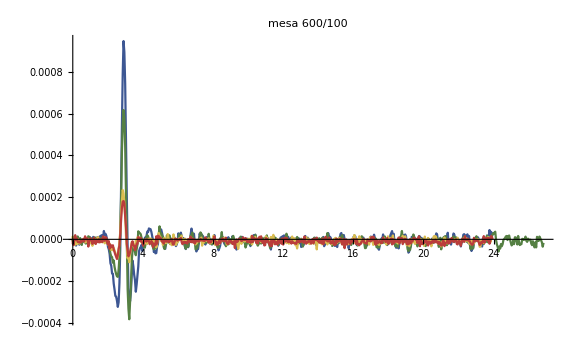
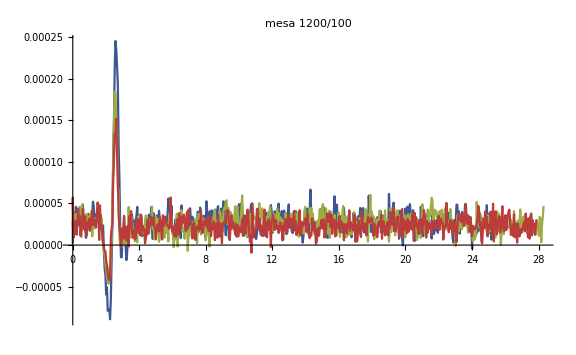

```mathematica
Row[
{ListLinePlot[Table[data11[[i,All,{3,2}]],{i,1,4}],PlotRange->All,ImageSize->Large,PlotStyle->"DarkRainbow",PlotLabel->"mesa 600/100"],
ListLinePlot[Table[data12[[i,All,{3,2}]],{i,1,3}],PlotRange->All,ImageSize->Large,PlotStyle->"DarkRainbow",PlotLabel->"mesa 1200/100"]}
]
```

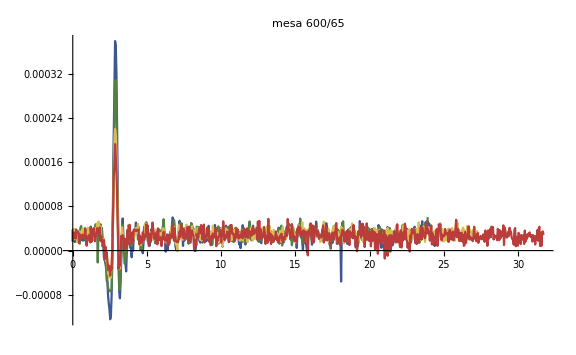

```mathematica
ListLinePlot[Table[data15[[i,All,{3,2}]],{i,1,4}],PlotRange->All,ImageSize->Large,PlotStyle->"DarkRainbow",PlotLabel->"mesa 600/65"]
```

```mathematica
FourierFilter
```

```mathematica
ClearAll[fourier11,fourier12,fourier15]
fourier11 = Table[Fourier[LowpassFilter[data11[[i,All,2]][[;;512]],50]],{i,1,4}];
fourier12 = Table[Fourier[LowpassFilter[data12[[i,All,2]][[;;512]],50]],{i,1,3}];
fourier15 = Table[Fourier[LowpassFilter[data15[[i,All,2]][[;;512]],50]],{i,1,4}];
```

```mathematica
frequency = Range[512]/data11[[1,512,3]];
```

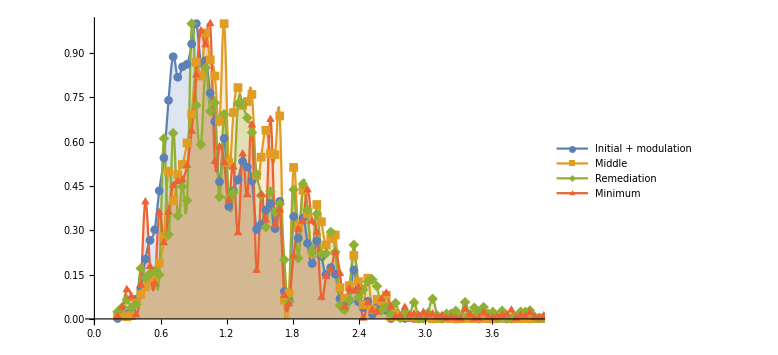

```mathematica
ListLinePlot[Table[Transpose[{frequency[[5;;]],Abs[fourier11[[i]][[5;;]]]^2/(Max[Abs[fourier11[[i]][[5;;]]]^2])}],{i,4}],PlotRange->{{0,4},All},ImageSize->Large,PlotLegends->{"Initial + modulation","Middle","Remediation","Minimum"},Filling->Bottom,InterpolationOrder->2,Mesh->Full,PlotMarkers->Automatic]
```

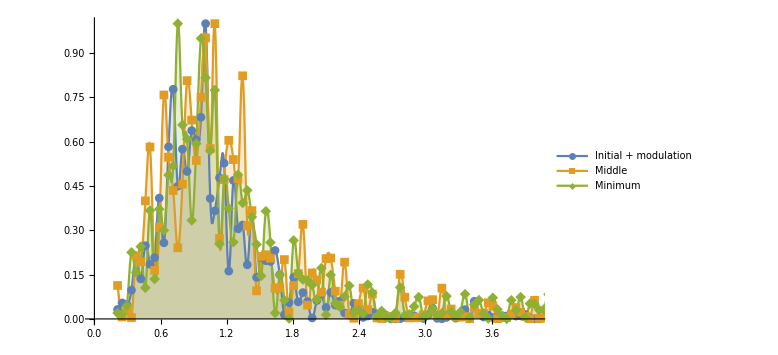

```mathematica
ListLinePlot[Table[Transpose[{frequency[[5;;]],Abs[fourier12[[i]][[5;;512]]]^2/(Max[Abs[fourier12[[i]][[5;;512]]]^2])}],{i,3}],PlotRange->{{0,4},All},ImageSize->Large,PlotLegends->{"Initial + modulation","Middle","Minimum"},Filling->Bottom,InterpolationOrder->2,Mesh->Full,PlotMarkers->Automatic]
```

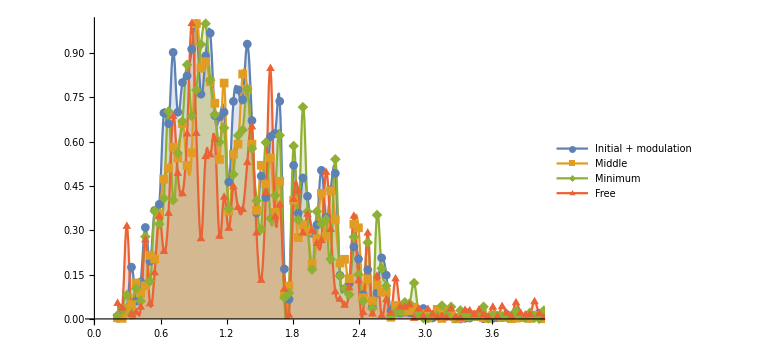

```mathematica
ListLinePlot[Table[Transpose[{frequency[[5;;]],Abs[fourier15[[i]][[5;;512]]]^2/(Max[Abs[fourier15[[i]][[5;;512]]]^2])}],{i,4}],PlotRange->{{0,4},All},ImageSize->Large,PlotLegends->{"Initial + modulation","Middle","Minimum","Free"},Filling->Bottom,InterpolationOrder->2,Mesh->Full,PlotMarkers->Automatic]
```